#### Homework 4 - Nikola Totev | FN 62271 | Group 6

```mathematica
(*Exercise 1*)
```

```mathematica
weight = 1;
approxPoly[x_]= a*x^2+b*x+c;
```

```mathematica
maxDiff[a_,b_,c_]:=(Integrate[weight*(Sin[x]-approxPoly[x])^2, {x,0, Pi/2}])^(1/2)
 
maxDiff[a,b,c]
√(4 a-2 c+1/4 (1+2 c^2) π+1/4 b c π^2+1/24 (b^2+2 a c) π^3+1/32 a b π^4+(a^2 π^5)/160-2 (b+a π))
```

```mathematica
derivativeByA[a_,b_,c_]= D[maxDiff[a,b,c],a];
derivativeByB[a_,b_,c_] =D[maxDiff[a,b,c],b];
derivativeByC[a_,b_,c_] =D[maxDiff[a,b,c],c];
```

```mathematica
coeficients = Solve[{derivativeByA[a,b,c]==0, derivativeByB[a,b,c]==0, derivativeByC[a,b,c]==0},{a,b,c}];

coeficients
{{a->(240 (-48+12 π+π^2))/π^5,b->-(48 (-120+28 π+3 π^2))/π^4,c->(6 (-80+16 π+3 π^2))/π^3}}
```

```mathematica
substitutedPoly[x_]=approxPoly[x]/.coeficients[[1]];

substitutedPoly[x]
(6 (-80+16 π+3 π^2))/π^3-(48 (-120+28 π+3 π^2) x)/π^4+(240 (-48+12 π+π^2) x^2)/π^5
```

```mathematica
functionsComparisonPlot = Plot[{Sin[x],substitutedPoly[x]}, {x, 0,Pi/2}, PlotLegends->"Expressions", PlotLabel->"Original vs Approximation", Filling->{1->{2}}];
```

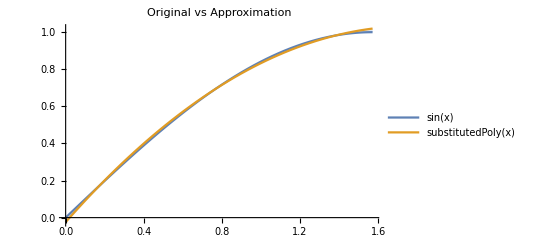

```mathematica
Show[functionsComparisonPlot]
```

```mathematica
(*Exercise 2*)
```

```mathematica
givenFunc[x_]:=x*E^(2x);
secondDeriv[x_] = D[givenFunc[x], {x,2}];
fourthDeriv[x_] = D[givenFunc[x], {x,4}];
a = 0;
b= 3;
expectedResult = N[(1(1+5 E^6))/4];
504.53599186
```

```mathematica
maxOfSecondDeriv  = Max[{secondDeriv[a], secondDeriv[b]}];
16 ⅇ^6;

maxOfFourthDeriv = Max[{fourthDeriv[a], fourthDeriv[b]}];
80 ⅇ^6;
```

Approximation using Gauss formula

Linear swap: x= 1.5*t + 1.5 & dx = 1.5*dt

```mathematica
givenFunctionWithLinearSwap[t_]:= 1.5*((1.5*t+1.5)*E^(2*(1.5*t+1.5)));
```

Using 2 nodes

```mathematica
twoNodeApproximation = givenFunctionWithLinearSwap[-1/(√3)]+givenFunctionWithLinearSwap[1/(√3)];
406.295021;
```

```mathematica
(*Calculation error*)
twoNodeError = Abs[ expectedResult - twoNodeApproximation]
98.24097028
```

Using 4 nodes

```mathematica
A1 = 0.347855;
A2=0.347855;
A3= 0.652145;
A4=0.652145;
```

```mathematica
x1 = -0.861136;
x2=0.861136;
x3=0.339981;
x4=-0.339981;
```

```mathematica
fourNodeApproximation = A1*givenFunctionWithLinearSwap[x1]+A2*givenFunctionWithLinearSwap[x2]+A3*givenFunctionWithLinearSwap[x3]+A4*givenFunctionWithLinearSwap[x4]
504.13021156
```

```mathematica
(*Calculation error*)
fourNodeError = Abs[expectedResult - fourNodeApproximation]
0.40578029
```

Approximation using Rectangle formula

```mathematica
RectApprox = N[(b-a)*givenFunc[(a+b)/2]]
90.384916
```

```mathematica
(*Calculation error*)
rectNodeError = Abs[expectedResult - RectApprox]
414.151075
```

Approximation using Trapezoid formula

```mathematica
TrapApprox = N[(b-a)/2*(givenFunc[a]+givenFunc[b])]
1815.42957071
```

```mathematica
(*Calculation error*)
trapNodeError = Abs[expectedResult - TrapApprox]
1310.893578
```

Approximation using Simpsons formula

```mathematica
SimpsonApprox= N[(b-a)*(givenFunc[a]+4*givenFunc[(a+b)/2]+givenFunc[b])]/6
665.399801
```

```mathematica
(*Calculation error*)
simpsNodeError = expectedResult - SimpsonApprox
-160.863809
```

```mathematica
(*Exercise 3*)
```

```mathematica
nodes = {0, Pi/4, Pi/2, (3*Pi)/4,Pi};
values = {1.0000,0.3431,0.2500,0.3431,1.0000};
```

```mathematica
integralApproximation = ∑_(i=2)^Length[nodes] ((nodes[[i]]-nodes[[i-1]])/2*(values[[i]]+values[[i-1]]))
1.52069
```